```mathematica
yyyHankRand[x_,y_,t_,k_,w_]=Sum[(BesselJ[0,k √(x^2+(y-d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y-d)^2)] Sin[w t]+BesselJ[0,k √(x^2+(y+d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y+d)^2)] Sin[w t])/(40),{d,7+RandomVariate[UniformDistribution[{-1,1}],20]}];
yyyHank[x_,y_,t_,k_,w_]=Sum[(BesselJ[0,k √(x^2+(y-d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y-d)^2)] Sin[w t]+BesselJ[0,k √(x^2+(y+d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y+d)^2)] Sin[w t])/(18),{d,7,11,0.5}];
```

```mathematica
DaForceX[x_,y_,t_,k_,w_] = -D[yyyHank[x,y,t,k,w],x];
DaForceY[x_,y_,t_,k_,w_] = -D[yyyHank[x,y,t,k,w],y];
DaForceTanhX[x_,y_,t_,k_,w_] = -Tanh[D[yyyHankRand[x,y,t,k,w],x]];
DaForceTanhY[x_,y_,t_,k_,w_] = -Tanh[D[yyyHankRand[x,y,t,k,w],y]];
CosDisSqWidth = ProbabilityDistribution[Cos[x]^2/2,{x,-π/2,π/2}]
AngleDis[σ_] =ProbabilityDistribution[ⅇ^(-ϕ^2/σ^2) Cos[ϕ]^2,{ϕ,-π/2,π/2}]
SincSqWidth[d_] = ProbabilityDistribution[Sinc[x π/(d)]^2/d,{x,-π/2,π/2}]
```

ProbabilityDistribution[Cos[x]^2/2,{x,-π/2,π/2}]

ProbabilityDistribution[ⅇ^(-x^2/σ^2) Cos[x]^2,{x,-π/2,π/2}]

ProbabilityDistribution[Sinc[(x π)/d]^2/d,{x,-π/2,π/2}]

```mathematica
yyyHank[x_,y_,t_,k_,w_]
```

1/18 (BesselJ[0,k_ √(x_^2+(-7.+y_)^2)] Cos[t_ w_]+BesselJ[0,k_ √(x_^2+(7.+y_)^2)] Cos[t_ w_]+BesselY[0,k_ √(x_^2+(-7.+y_)^2)] Sin[t_ w_]+BesselY[0,k_ √(x_^2+(7.+y_)^2)] Sin[t_ w_])+1/18 (BesselJ[0,k_ √(x_^2+(-7.5+y_)^2)] Cos[t_ w_]+BesselJ[0,k_ √(x_^2+(7.5+y_)^2)] Cos[t_ w_]+BesselY[0,k_ √(x_^2+(-7.5+y_)^2)] Sin[t_ w_]+BesselY[0,k_ √(x_^2+(7.5+y_)^2)] Sin[t_ w_])+1/18 (BesselJ[0,k_ √(x_^2+(-8.+y_)^2)] Cos[t_ w_]+BesselJ[0,k_ √(x_^2+(8.+y_)^2)] Cos[t_ w_]+BesselY[0,k_ √(x_^2+(-8.+y_)^2)] Sin[t_ w_]+BesselY[0,k_ √(x_^2+(8.+y_)^2)] Sin[t_ w_])+1/18 (BesselJ[0,k_ √(x_^2+(-8.5+y_)^2)] Cos[t_ w_]+BesselJ[0,k_ √(x_^2+(8.5+y_)^2)] Cos[t_ w_]+BesselY[0,k_ √(x_^2+(-8.5+y_)^2)] Sin[t_ w_]+BesselY[0,k_ √(x_^2+(8.5+y_)^2)] Sin[t_ w_])+1/18 (BesselJ[0,k_ √(x_^2+(-9.+y_)^2)] Cos[t_ w_]+BesselJ[0,k_ √(x_^2+(9.+y_)^2)] Cos[t_ w_]+BesselY[0,k_ √(x_^2+(-9.+y_)^2)] Sin[t_ w_]+BesselY[0,k_ √(x_^2+(9.+y_)^2)] Sin[t_ w_])+1/18 (BesselJ[0,k_ √(x_^2+(-9.5+y_)^2)] Cos[t_ w_]+BesselJ[0,k_ √(x_^2+(9.5+y_)^2)] Cos[t_ w_]+BesselY[0,k_ √(x_^2+(-9.5+y_)^2)] Sin[t_ w_]+BesselY[0,k_ √(x_^2+(9.5+y_)^2)] Sin[t_ w_])+1/18 (BesselJ[0,k_ √(x_^2+(-10.+y_)^2)] Cos[t_ w_]+BesselJ[0,k_ √(x_^2+(10.+y_)^2)] Cos[t_ w_]+BesselY[0,k_ √(x_^2+(-10.+y_)^2)] Sin[t_ w_]+BesselY[0,k_ √(x_^2+(10.+y_)^2)] Sin[t_ w_])+1/18 (BesselJ[0,k_ √(x_^2+(-10.5+y_)^2)] Cos[t_ w_]+BesselJ[0,k_ √(x_^2+(10.5+y_)^2)] Cos[t_ w_]+BesselY[0,k_ √(x_^2+(-10.5+y_)^2)] Sin[t_ w_]+BesselY[0,k_ √(x_^2+(10.5+y_)^2)] Sin[t_ w_])+1/18 (BesselJ[0,k_ √(x_^2+(-11.+y_)^2)] Cos[t_ w_]+BesselJ[0,k_ √(x_^2+(11.+y_)^2)] Cos[t_ w_]+BesselY[0,k_ √(x_^2+(-11.+y_)^2)] Sin[t_ w_]+BesselY[0,k_ √(x_^2+(11.+y_)^2)] Sin[t_ w_])

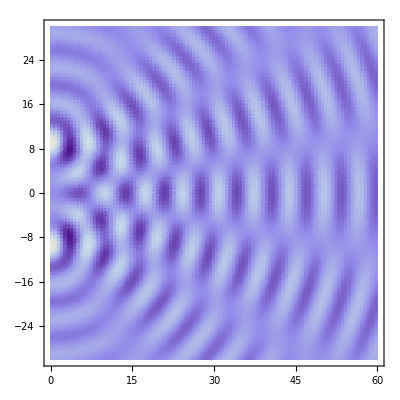

```mathematica
DensityPlot[yyyHank[x,y,0,1,1],{x,0,60},{y,-30,30},PlotPoints->{100,100},ClippingStyle->Automatic,BaseStyle->{FontFamily->"Times",FontSize->14},AspectRatio->1]
```

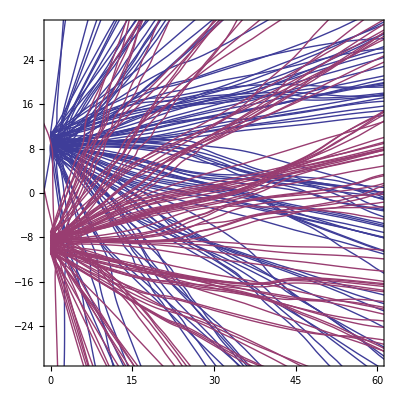

```mathematica
AAA =  1.0;
ddd = 9.0;
www = 1.0;
x000 = 0.0;
v000 = 1.0;
kkk= 1.0;
disss = 0.005;
tmax = 250;
xmax = 60;
NMAX=100;
swidth = 2;
phase = -1/2.0;

Hollandtabl3DU=
Parallelize[Table[NDSolve[{D[x[t],t,t] ==  AAA DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA DaForceY[x[t],y[t],t+phase,kkk,www]-disss  D[y[t],t],y[0]== ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[SincSqWidth[2.0]]],x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{NMAX}]
];
Hollandtabl3DD=
Parallelize[Table[NDSolve[{D[x[t],t,t] ==  AAA  DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA  DaForceY[x[t],y[t],t+phase,kkk,www]-disss D[y[t],t],y[0]== -ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[SincSqWidth[2.0]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{NMAX}]
];
ParametricPlot[{{x[t],y[t]}/.Hollandtabl3DU,{x[t],y[t]}/.Hollandtabl3DD},{t,0,tmax},PlotRange->{{0,xmax},{-xmax/2,xmax/2}},Frame->True,Axes->True, AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

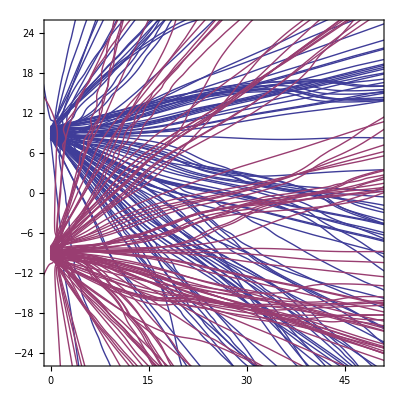

```mathematica
AAA = 10.0;
ddd = 7.0;
www = 1;
x000 = 0.0;
v000 = 1;
kkk=1;
q=NDSolve[{D[x[t],t,t] ==  AAA  DaForceX[x[t],y[t],t,kkk,www], D[y[t],t,t] == AAA  DaForceY[x[t],y[t],t,kkk,www],y[0]== -ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[SincSqWidth[1.5]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
```

{{x→InterpolatingFunction[{{0.,60.}},<>],y→InterpolatingFunction[{{0.,60.}},<>]}}

```mathematica
ss=Table[Show[{DensityPlot[{yyyHankRand[x,y,t,1,1] },{x,0,30},{y,-15,15},PlotRange->{Full,Full},PlotPoints->{50,50}, ImageSize->{500,500},PlotLegends->Automatic],ParametricPlot[{{x[g],y[g]}/.q},{g,0,t+0.001},PlotStyle->Thick]}],{t,0,10,1.0}];
```

```mathematica
ListAnimate[ss,AnimationRunning->True]
```

```mathematica
AAA =  1.0;
ddd = 9.0;
www = 1.0;
x000 = 0.0;
v000 = 1.0;
kkk= 1.0;
disss = 0.005;
tmax = 100;
swidth = 1;
CHUNK = 100;
REPEAT = 1000;
CUTTOFF = 40;
phase = -1/2.0;
MEMORY = 6.5;

outstream=OpenAppend["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitPhaseC40PM05D9W2M65.dat"];

Do[
Parallelize[
Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] == ⅇ^(-t/MEMORY)( AAA DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] ==ⅇ^(-t/MEMORY)( AAA DaForceY[x[t],y[t],t+phase,kkk,www]-disss  D[y[t],t]),y[0]== ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[SincSqWidth[1.5]]],x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{CHUNK}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  ⅇ^(-t/MEMORY)(AAA  DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] == ⅇ^(-t/MEMORY)(AAA  DaForceY[x[t],y[t],t+phase,kkk,www]-disss D[y[t],t]),y[0]== -ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[SincSqWidth[1.5]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{CHUNK}];
];


TestTableXU[t_] = Flatten[x[t]/.Hollandtabl3DU];
TestTableYU[t_] = Flatten[y[t]/.Hollandtabl3DU];
TestTableXD[t_] = Flatten[x[t]/.Hollandtabl3DD];
TestTableYD[t_] = Flatten[y[t]/.Hollandtabl3DD];

HistTableAngle = {};
For[NNN = 1,NNN<=Length[TestTableXU[qqq]],NNN++,
For[ttt=1,ttt < tmax, ttt++, If[(TestTableXU[ttt][[NNN]]^2+TestTableYU[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYU[ttt][[NNN]]/TestTableXU[ttt][[NNN]]]];Break[]]]
]
For[NNN = 1,NNN<=Length[TestTableXD[qqq]],NNN++,
For[ttt=1,ttt < tmax, ttt++, If[(TestTableXD[ttt][[NNN]]^2+TestTableYD[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYD[ttt][[NNN]]/TestTableXD[ttt][[NNN]]]];Break[]]]
];

Export[outstream,HistTableAngle]

WriteString[outstream,"\n"]
,{REPEAT}];

Close[outstream]
```

$Aborted

/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitPhaseC40PM05D9W2M65.dat

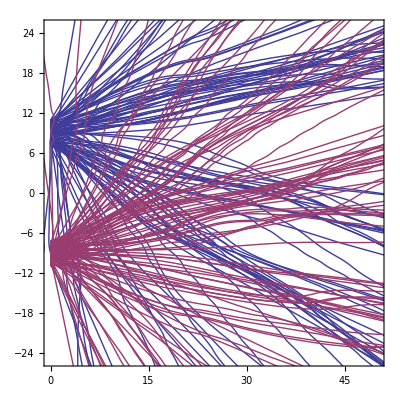

```mathematica
AAA =  1.0;
ddd = 9.0;
www = 1.0;
x000 = 0.0;
v000 = 1.0;
kkk= 1.0;
disss = 0.005;
tmax = 250;
xmax = 60;
NMAX=100;
swidth = 2;
phase = -1/2.0;
MEMORY = 1000;

Parallelize[
Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] == ⅇ^(-t/MEMORY)( AAA DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] ==ⅇ^(-t/MEMORY)( AAA DaForceY[x[t],y[t],t+phase,kkk,www]-disss  D[y[t],t]),y[0]== ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[CosDisSqWidth]],x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{NMAX}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  ⅇ^(-t/MEMORY)(AAA  DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] == ⅇ^(-t/MEMORY)(AAA  DaForceY[x[t],y[t],t+phase,kkk,www]-disss D[y[t],t]),y[0]== -ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[CosDisSqWidth]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{NMAX}];
];

ParametricPlot[{{x[t],y[t]}/.Hollandtabl3DU,{x[t],y[t]}/.Hollandtabl3DD},{t,0,tmax},PlotRange->{{0,xmax},{-xmax/2,xmax/2}},Frame->True,Axes->True, AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

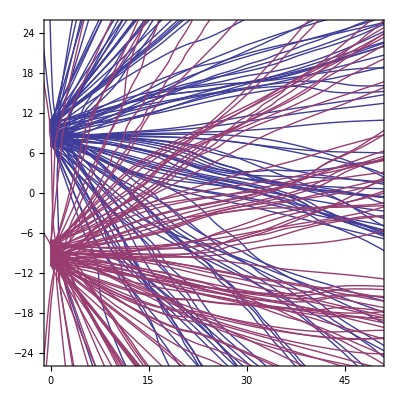

```mathematica
AAA =  1.0;
ddd = 9.0;
www = 1.0;
x000 = 0.0;
v000 = 1.0;
kkk= 1.0;
disss = 0.005;
tmax = 100;
swidth = 2;
CHUNK = 100;
REPEAT = 1000;
CUTTOFF = 40;
phase = -1/2.0;
MEMORY = 40;

outstream=OpenAppend["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitPhaseCosC40M40W2.dat"];

Do[
Parallelize[
Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] == ⅇ^(-t/MEMORY)( AAA DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] ==ⅇ^(-t/MEMORY)( AAA DaForceY[x[t],y[t],t+phase,kkk,www]-disss  D[y[t],t]),y[0]== ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[CosDisSqWidth]],x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{CHUNK}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  ⅇ^(-t/MEMORY)(AAA  DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] == ⅇ^(-t/MEMORY)(AAA  DaForceY[x[t],y[t],t+phase,kkk,www]-disss D[y[t],t]),y[0]== -ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[CosDisSqWidth]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{CHUNK}];
];


TestTableXU[t_] = Flatten[x[t]/.Hollandtabl3DU];
TestTableYU[t_] = Flatten[y[t]/.Hollandtabl3DU];
TestTableXD[t_] = Flatten[x[t]/.Hollandtabl3DD];
TestTableYD[t_] = Flatten[y[t]/.Hollandtabl3DD];

HistTableAngle = {};
For[NNN = 1,NNN<=Length[TestTableXU[qqq]],NNN++,
For[ttt=1,ttt < tmax, ttt++, If[(TestTableXU[ttt][[NNN]]^2+TestTableYU[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYU[ttt][[NNN]]/TestTableXU[ttt][[NNN]]]];Break[]]]
]
For[NNN = 1,NNN<=Length[TestTableXD[qqq]],NNN++,
For[ttt=1,ttt < tmax, ttt++, If[(TestTableXD[ttt][[NNN]]^2+TestTableYD[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYD[ttt][[NNN]]/TestTableXD[ttt][[NNN]]]];Break[]]]
];

Export[outstream,HistTableAngle]

WriteString[outstream,"\n"]
,{REPEAT}];

Close[outstream]
```

$Aborted

/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitPhaseCosC40M40W2.dat

```mathematica
AAA =  1.0;
ddd = 9.0;
www = 1.0;
x000 = 0.0;
v000 = 1.0;
kkk= 1.0;
disss = 0.005;
tmax = 100;
swidth = 2;
CHUNK = 100;
REPEAT = 1000;
CUTTOFF = 40;
phase = -1/2.0;
MEMORYLIST = {1,2.5,5,7.5,10,12.5,15,20,30,40};
MEMORYLIST = {10,15};

Do[
Close["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitAuto2M"<> ToString[MEMVALUE]<>".dat"]
,{MEMVALUE,MEMORYLIST}]

Do[
Do[
outstream=OpenAppend["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitAuto2M"<> ToString[MEMVALUE]<>".dat"];

Parallelize[
Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] == ⅇ^(-t/MEMVALUE)( AAA DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] ==ⅇ^(-t/MEMVALUE)( AAA DaForceY[x[t],y[t],t+phase,kkk,www]-disss  D[y[t],t]),y[0]== ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[CosDisSqWidth]],x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{CHUNK}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  ⅇ^(-t/MEMVALUE)(AAA  DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] == ⅇ^(-t/MEMVALUE)(AAA  DaForceY[x[t],y[t],t+phase,kkk,www]-disss D[y[t],t]),y[0]== -ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[CosDisSqWidth]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{CHUNK}];
];


TestTableXU[t_] = Flatten[x[t]/.Hollandtabl3DU];
TestTableYU[t_] = Flatten[y[t]/.Hollandtabl3DU];
TestTableXD[t_] = Flatten[x[t]/.Hollandtabl3DD];
TestTableYD[t_] = Flatten[y[t]/.Hollandtabl3DD];

HistTableAngle = {};
For[NNN = 1,NNN<=Length[TestTableXU[qqq]],NNN++,
For[ttt=20,ttt < tmax, ttt+=0.1, If[(TestTableXU[ttt][[NNN]]^2+TestTableYU[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYU[ttt][[NNN]]/TestTableXU[ttt][[NNN]]]];Break[]]]
]
For[NNN = 1,NNN<=Length[TestTableXD[qqq]],NNN++,
For[ttt=20,ttt < tmax, ttt+=0.1, If[(TestTableXD[ttt][[NNN]]^2+TestTableYD[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYD[ttt][[NNN]]/TestTableXD[ttt][[NNN]]]];Break[]]]
];

Export[outstream,HistTableAngle]

WriteString[outstream,"\n"]
Close[outstream]

(*Beep[]*)
EmitSound[Play[Sin[1000 t^2],{t,0,1}]];

,{MEMVALUE,MEMORYLIST}];
(*Close[outstream]*)
,{REPEAT}];
```

General::openx: "/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitAuto2M10.dat" is not open.

$Aborted

```mathematica
AAA =  1.0;
ddd = 9.0;
www = 1.0;
x000 = 0.0;
v000 = 1.0;
kkk= 1.0;
disss = 0.005;
tmax = 120;
swidth = 2;
CHUNK = 100;
REPEAT = 1000;
CUTTOFF = 80;
phase = -1/2.0;
MEMORYLIST = {1,2.5,5,7.5,10,12.5,15,20,30,40};
MEMORYLIST = {40};

Do[
Close["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitAutoC80M"<> ToString[MEMVALUE]<>".dat"]
,{MEMVALUE,MEMORYLIST}]

Do[
Do[
outstream=OpenAppend["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitAutoC80M"<> ToString[MEMVALUE]<>".dat"];

Parallelize[
Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] == ⅇ^(-t/MEMVALUE)( AAA DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] ==ⅇ^(-t/MEMVALUE)( AAA DaForceY[x[t],y[t],t+phase,kkk,www]-disss  D[y[t],t]),y[0]== ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[CosDisSqWidth]],x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{CHUNK}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  ⅇ^(-t/MEMVALUE)(AAA  DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] == ⅇ^(-t/MEMVALUE)(AAA  DaForceY[x[t],y[t],t+phase,kkk,www]-disss D[y[t],t]),y[0]== -ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[CosDisSqWidth]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{CHUNK}];
];


TestTableXU[t_] = Flatten[x[t]/.Hollandtabl3DU];
TestTableYU[t_] = Flatten[y[t]/.Hollandtabl3DU];
TestTableXD[t_] = Flatten[x[t]/.Hollandtabl3DD];
TestTableYD[t_] = Flatten[y[t]/.Hollandtabl3DD];

HistTableAngle = {};
For[NNN = 1,NNN<=Length[TestTableXU[qqq]],NNN++,
For[ttt=40,ttt < tmax, ttt+=0.1, If[(TestTableXU[ttt][[NNN]]^2+TestTableYU[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYU[ttt][[NNN]]/TestTableXU[ttt][[NNN]]]];Break[]]]
]
For[NNN = 1,NNN<=Length[TestTableXD[qqq]],NNN++,
For[ttt=40,ttt < tmax, ttt+=0.1, If[(TestTableXD[ttt][[NNN]]^2+TestTableYD[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYD[ttt][[NNN]]/TestTableXD[ttt][[NNN]]]];Break[]]]
];

Export[outstream,HistTableAngle]

WriteString[outstream,"\n"]
Close[outstream]
,{MEMVALUE,MEMORYLIST}];
(*Close[outstream]*)
,{REPEAT}];
```

$Aborted